```mathematica
ClearAll["Global`*"];
Lmin = 0;
Lmax = +1;
Vmin = -10;
Vmax = +10;
nx = 1;
kx = 2 Pi/((Lmax - Lmin)/nx);
nv = 2;
kv =  2 Pi/((Vmax - Vmin)/nv);
w =1;
LevX=4;
LevV=4;
Deg=3;
dt=N[Lmax/(2^LevX)/Vmax(2*Deg+1)]
nt=100;
fx:= Sin[kx x ];
ft:= Sin[w t];
fv:= Sin[kv v];
f:=fx fv ft;
Ex:=Cos[kx x];
Et:=Cos[w t];
EE:=Ex Et;
f
fx[Lmin]
0.04375
Sin[t] Sin[(π v)/5] Sin[2 π x]
Sin[2 π x][0]
```

0.04375

Sin[t] Sin[(π v)/5] Sin[2 π x]

Sin[2 π x][0]

0.04375

Sin[t] Sin[(π v)/5] Sin[2 π x]

Sin[2 π x][0]

```mathematica
source1=D[f,t]
source2=v D[f,x]
source3 = EE D[f,v]
dt*nt
```

Cos[t] Sin[(π v)/5] Sin[2 π x]

2 π v Cos[2 π x] Sin[t] Sin[(π v)/5]

1/5 π Cos[t] Cos[(π v)/5] Cos[2 π x] Sin[t] Sin[2 π x]

4.375

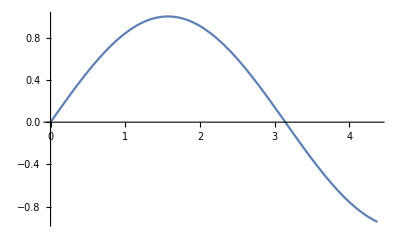

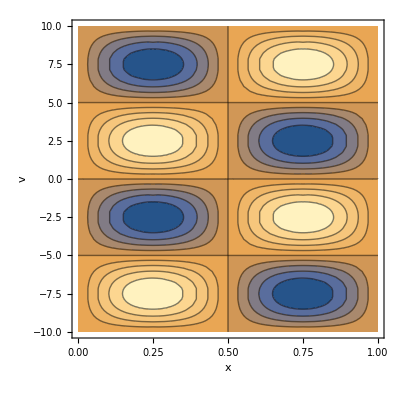

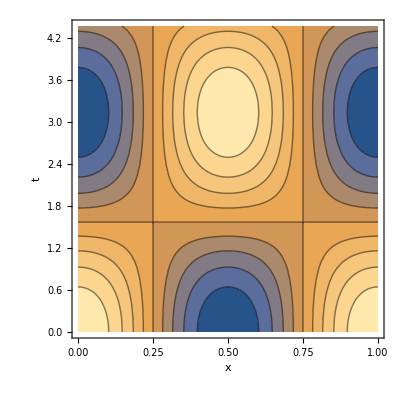

```mathematica
Plot[ft,{t,0,nt dt}]
t=0.1;
ContourPlot[f,{x,Lmin,Lmax},{v,Vmin,Vmax},FrameLabel->Automatic]
ContourPlot[EE,{x,Lmin,Lmax},{t,0,nt dt},FrameLabel->Automatic]
```

## continuity1 test case (1D)

```mathematica
ClearAll["Global`*"];
D[f[x,t],t]+v D[f[x,t],x]==0 // Defer // TraditionalForm
```

v (∂f(x,t))/(∂x)+(∂f(x,t))/(∂t)==0

```mathematica
xMin=-1;
xMax=+1;
ft=Sin[w t]; 
fx=Cos[k x];
w=1;
n=2;
v=1;
k=2 Pi/((xMax-xMin)/n);
f=ft fx;
source1=D[f,t]
source2=v D[f,x]
```

Cos[t] Cos[2 π x]

-2 π Sin[t] Sin[2 π x]

```mathematica
-2 π Sin[t] Sin[2 π x]
```

## continuity2 test case (2D)

```mathematica
ClearAll["Global`*"];
D[f[x,y,t],t]+Subscript[v, x] D[f[x,y,t],x]+Subscript[v, y] D[f[x,y,t],y]==0 // Defer // TraditionalForm
```

v_x (∂f(x,y,t))/(∂x)+v_y (∂f(x,y,t))/(∂y)+(∂f(x,y,t))/(∂t)==0

```mathematica
xMin=-1;
xMax=+1;
yMin=-2;
yMax=+2;
ft=Sin[w t];
fx=Cos[kx x];
fy=Sin[ky y];
w=2;
nx=1;
ny=4;
vx=1;
vy=1;
kx=2 Pi/((xMax-xMin)/nx);
ky=2 Pi/((yMax-yMin)/ny);
v={vx,vy};
f=fx fy ft;
StringForm["Analytic solution: f(x,y,t)=``",f]
source1=D[f,t];
source2=v.Grad[f,{x,y}];
StringForm["Source 1: ``",source1]
StringForm["Source 2: ``",source2[[1]]]
StringForm["Source 3: ``",source2[[2]]]
t=0;
StringForm["Initial condition: f(x,y,z,t)=``",f]
```

Analytic solution: f(x,y,t)=Cos[π x] Sin[2 t] Sin[2 π y]

Source 1: 2 Cos[2 t] Cos[π x] Sin[2 π y]

Source 2: 2 π Cos[π x] Cos[2 π y] Sin[2 t]

Source 3: -π Sin[2 t] Sin[π x] Sin[2 π y]

Initial condition: f(x,y,z,t)=0

## continuity3 test case (3D)

```mathematica
ClearAll["Global`*"];
D[f[x,y,z,t],t]+Subscript[v, x] D[f[x,y,z,t],x]+Subscript[v, y] D[f[x,y,z,t],y]+Subscript[v, z] D[f[x,y,z,t],z]==0 // Defer // TraditionalForm
xMin=-1;
xMax=+1;
yMin=-2;
yMax=+2;
zMin=-3;
zMax=+3;
ft=Sin[w t];
fx=Cos[kx x];
fy=Sin[ky y];
fz=Cos[kz z];
w=2;
nx=1;
ny=4;
nz=2;
vx=1;
vy=1;
vz=3;
kx=2 Pi/((xMax-xMin)/nx);
ky=2 Pi/((yMax-yMin)/ny);
kz=2 Pi/((zMax-zMin)/nz);
v={vx,vy,vz};
f=fx fy fz ft;
StringForm["Analytic solution: f(x,y,z,t)=``",f]
source1=D[f,t];
source2=v.Grad[f,{x,y,z}];
StringForm["Source 1: ``",source1]
StringForm["Source 2: ``",source2[[1]]]
StringForm["Source 3: ``",source2[[2]]]
StringForm["Source 4: ``",source2[[3]]]
t=0;
StringForm["Initial condition: f(x,y,z,t)=``",f]
```

v_x (∂f(x,y,z,t))/(∂x)+v_y (∂f(x,y,z,t))/(∂y)+v_z (∂f(x,y,z,t))/(∂z)+(∂f(x,y,z,t))/(∂t)==0

Analytic solution: f(x,y,z,t)=Cos[π x] Cos[(2 π z)/3] Sin[2 t] Sin[2 π y]

Source 1: 2 Cos[2 t] Cos[π x] Cos[(2 π z)/3] Sin[2 π y]

Source 2: 2 π Cos[π x] Cos[2 π y] Cos[(2 π z)/3] Sin[2 t]

Source 3: -π Cos[(2 π z)/3] Sin[2 t] Sin[π x] Sin[2 π y]

Source 4: -2 π Cos[π x] Sin[2 t] Sin[2 π y] Sin[(2 π z)/3]

Initial condition: f(x,y,z,t)=0

## continuity6 test case (6D)

a_x (∂F)/(∂v_x)+a_y (∂F)/(∂v_y)+a_z (∂F)/(∂v_z)+b_x (∂F)/(∂x)+b_y (∂F)/(∂y)+b_z (∂F)/(∂z)+(∂F)/(∂t)==0

Analytic solution: f(x,y,z,v_x,v_y,v_z,t)=Cos[(π vx)/10] Cos[(π vz)/30] Cos[π x] Cos[(π z)/3] Sin[2 t] Sin[(π vy)/20] Sin[(π y)/2]

Source 0: 2 Cos[2 t] Cos[(π vx)/10] Cos[(π vz)/30] Cos[π x] Cos[(π z)/3] Sin[(π vy)/20] Sin[(π y)/2]

Source 1: 1/2 π Cos[(π vx)/10] Cos[(π vz)/30] Cos[π x] Cos[(π y)/2] Cos[(π z)/3] Sin[2 t] Sin[(π vy)/20]

Source 2: -π Cos[(π vx)/10] Cos[(π vz)/30] Cos[(π z)/3] Sin[2 t] Sin[(π vy)/20] Sin[π x] Sin[(π y)/2]

Source 3: -π Cos[(π vx)/10] Cos[(π vz)/30] Cos[π x] Sin[2 t] Sin[(π vy)/20] Sin[(π y)/2] Sin[(π z)/3]

Source 4: 3/20 π Cos[(π vx)/10] Cos[(π vy)/20] Cos[(π vz)/30] Cos[π x] Cos[(π z)/3] Sin[2 t] Sin[(π y)/2]

Source 5: -2/5 π Cos[(π vz)/30] Cos[π x] Cos[(π z)/3] Sin[2 t] Sin[(π vx)/10] Sin[(π vy)/20] Sin[(π y)/2]

Source 6: -1/15 π Cos[(π vx)/10] Cos[π x] Cos[(π z)/3] Sin[2 t] Sin[(π vy)/20] Sin[(π vz)/30] Sin[(π y)/2]

Initial condition: f(x,y,z,v_x,v_y,v_z,t)=0

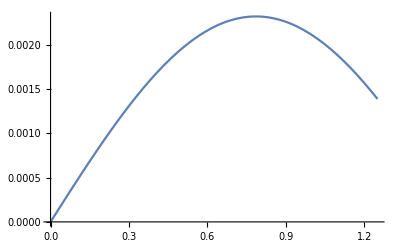

```mathematica
ClearAll["Global`*"];
(*F:=f[x,y,z,Subscript[v, x],Subscript[v, y],Subscript[v, z],t];*)
D[F,t]+Subscript[b, x] D[F,x]+Subscript[b, y] D[F,y]+Subscript[b, z] D[F,z]+Subscript[a, x] D[F,Subscript[v, x]]+Subscript[a, y] D[F,Subscript[v, y]]+Subscript[a, z] D[F,Subscript[v, z]]==0 // Defer // TraditionalForm
xMin=-1;
xMax=+1;
yMin=-2;
yMax=+2;
zMin=-3;
zMax=+3;
vxMin=-10;
vxMax=+10;
vyMin=-20;
vyMax=+20;
vzMin=-30;
vzMax=+30;
ft=Sin[w t];
fx=Cos[kx x];
fy=Sin[ky y];
fz=Cos[kz z];
fvx=Cos[kvx vx];
fvy=Sin[kvy vy];
fvz=Cos[kvz vz];
w=2;
nx=1;
ny=1;
nz=1;
nvx=1;
nvy=1;
nvz=1;
bx=1;
by=1;
bz=3;
ax=4;
ay=3;
az=2;
kx=2 Pi/((xMax-xMin)/nx);
ky=2 Pi/((yMax-yMin)/ny);
kz=2 Pi/((zMax-zMin)/nz);
kvx=2 Pi/((vxMax-vxMin)/nvx);
kvy=2 Pi/((vyMax-vyMin)/nvy);
kvz=2 Pi/((vzMax-vzMin)/nvz);
vv={bx,by,bz};
aa={ax,ay,az};
f=fx fy fz fvx fvy fvz ft;
StringForm["Analytic solution: f(x,y,z,v_x,v_y,v_z,t)=``",f]
source1=D[f,t];
source2=vv.Grad[f,{x,y,z}];
source3=aa.Grad[f,{vx,vy,vz}];
StringForm["Source 0: ``",source1]
StringForm["Source 1: ``",source2[[1]]]
StringForm["Source 2: ``",source2[[2]]]
StringForm["Source 3: ``",source2[[3]]]
StringForm["Source 4: ``",source3[[1]]]
StringForm["Source 5: ``",source3[[2]]]
StringForm["Source 6: ``",source3[[3]]]
t=0;
StringForm["Initial condition: f(x,y,z,v_x,v_y,v_z,t)=``",f]
dt=0.0125;
nt=100;
vx=0.1;
vy=0.1;
vz=0.1;
x=0.1;
y=0.1;
z=0.1;
Plot[f,{t,0,nt dt}]
(*t=0.1;
ContourPlot[f,{x,Lmin,Lmax},{v,Vmin,Vmax},FrameLabel->Automatic]
ContourPlot[EE,{x,Lmin,Lmax},{t,0,nt dt},FrameLabel->Automatic]*)
```

## fokkerplanck2_6p1

```mathematica
ClearAll["Global`*"];
a=2;
Q=Integrate[ 4/(Sqrt[Pi] a^3) Exp[-p^2/a^2],{p,0.001,10}];
dfdp = D[Q 4/(Sqrt[Pi] a^3) Exp[-p^2/a^2],p];
Q
p=0.01;
dfdp
```

0.499718

-0.000704821

## seperable_adapt _test_2d

```mathematica
ClearAll["Global`*"];
D[f[x,y,t],t]+Subscript[v, x] D[f[x,y,t],x]==0 // Defer // TraditionalForm
```

v_x (∂f(x,y,t))/(∂x)+(∂f(x,y,t))/(∂t)==0

Analytic solution: f(x,y,t)=ⅇ^(-(x-Sin[t])^2/w) x

Analytic solution: f(x,y,t)=-CC ⅇ^(-(x-Sin[t])^2/w) Sin[2 π y]

Source T1 part 1 : (2 ⅇ^(-(x-Sin[t])^2/w) x^2 Cos[t])/w

Source T1 part 2 : -(2 ⅇ^(-(x-Sin[t])^2/w) x Cos[t] Sin[t])/w

Source T2 part 1 : ⅇ^(-(x-Sin[t])^2/w)

Source T2 part 2 : -(2 ⅇ^(-(x-Sin[t])^2/w) x^2)/w

Source T2 part 3 : (2 ⅇ^(-(x-Sin[t])^2/w) x Sin[t])/w

Source2 T1 part 1 : -(2 CC ⅇ^(-(x-Sin[t])^2/w) x Cos[t] Sin[2 π y])/w

Source2 T1 part 2 : (2 CC ⅇ^(-(x-Sin[t])^2/w) Cos[t] Sin[t] Sin[2 π y])/w

Source2 T2 part 1 : (2 CC ⅇ^(-(x-Sin[t])^2/w) x Sin[2 π y])/w

Source2 T2 part 2 : -(2 CC ⅇ^(-(x-Sin[t])^2/w) Sin[t] Sin[2 π y])/w

Initial condition 1: f(x,y,z,t)=ⅇ^(-x^2/w) x

Initial condition 2: f(x,y,z,t)=-CC ⅇ^(-x^2/w) Sin[2 π y]

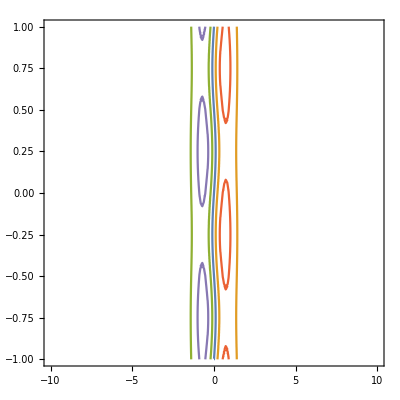

```mathematica
ClearAll["Global`*"];
(*  (xx-yy*0.1).*exp(-(xx-5).^2)  *)
(*   x*exp(-(x-offset(t))^2 - C*y*exp(-(x-offset(t))^2  *)
(*   part1                     part2                     *)
 
ft=1;
offset = Sin[ t];
expf = Exp[-(x-offset)^2/w];
(*   part 1   *)  
fx=x expf;
fy=1;
vx=1;
f=fx fy ft;
(*   part 2   *)  
fx2 = expf;
fy2=-CC Sin[2 Pi y];
f2=fx2 fy2 ft;
StringForm["Analytic solution: f(x,y,t)=``",f]
StringForm["Analytic solution: f(x,y,t)=``",f2]
sourceT1=Expand[D[f,t]];
sourceT2=Expand[vx D[f,x]];
For[i=1,i<=Length[sourceT1],i++,Print[StringForm["Source T1 part `` : ``",i,sourceT1[[i]]]]];
For[i=1,i<=Length[sourceT2],i++,Print[StringForm["Source T2 part `` : ``",i,sourceT2[[i]]]]];
source2T1=Expand[D[f2,t]];
source2T2=Expand[vx D[f2,x]];
For[i=1,i<=Length[source2T1],i++,Print[StringForm["Source2 T1 part `` : ``",i,source2T1[[i]]]]];
For[i=1,i<=Length[source2T2],i++,Print[StringForm["Source2 T2 part `` : ``",i,source2T2[[i]]]]];
t=0;
StringForm["Initial condition 1: f(x,y,z,t)=``",f]
StringForm["Initial condition 2: f(x,y,z,t)=``",f2]
w=1;
CC = 0.1;
ff=f+f2;
ContourPlot[{ff==0,ff==0.2,ff==-0.2,ff==0.4,ff==-0.4,ff==0.6,ff==-0.6},{x,-10,10},{y,-1,1}]
```